Clear Variables

```mathematica
Clear["Global`*"]
```

Calculations

```mathematica
Mf=.2594;(*final mass/mass of rocket w/o fuel in kg*)
Mi=.2702;(*initial mass/mass of rocket w/fuel in kg*)
ttThrust=3.1;(*total time*)
dt=1;(*time step*)
dm=(Mi-Mf)/ttThrust;(*change in mass*)
Ve=2482;(*exhaust velocity of C6-0 model rocket*)
A=0.00164748;(*in m*)
Thrust=14.1;
(*in newtons/max thrust of C6-0 model rocket*)

g=9.81;(*gravitational constant on Earth near the surface*)
Fg[t_]=Mc[t]*g;(*Force of gravity on the rocket over time*)
Cd=0.75;
p=0.74;
Fd[t_]=0.5*Cd*p*A*(Vf[t]^2);

Fnet[t_]=Thrust-(Fg[t]+Fd[t]);
a[t_]=Fnet[t]/Mc[t];

Mc[t_]:=Mi-(dm*t);(*current mass function*)
Vf[t_]:=Log[Mi/(Mc[t]-dm)]*Ve;(*velocity function*)
eqns={pos''[t]==a[t],pos'[0]==0,pos[0]==0};
{xs,vs}=NDSolveValue[eqns,{pos,pos'},{t,0,ttThrust}];
(*acceleration goes negative if rocket cannot sustain flight*)

(*-------------------------------------------------------------------------*)

(*NO THRUST CALCULATIONS*)
i1NT=Integrate[vs[t],{t,0,ttThrust}];
startHeightNT=N[i1NT];

ttToMaxHeight=1;

DRAG=(Cd*p*A)/2;
VNT=vs[ttThrust];
ANT=a[ttThrust];
XNT=startHeightNT;
listOfANT={};
listOfVNT={};
listOfXNT={};

l=1;
While[l==1,ttToMaxHeight+=dt;
{Acurrent =(-DRAG/Mf)*(VNT*VNT)-g,Vcurrent=VNT+Acurrent,If[Vcurrent<=0,Break[],l=1]};
ANT=(-DRAG/Mf)*(VNT*VNT)-g;
{VNT=VNT+ANT,
XNT=XNT+VNT,
listOfANT=Append[listOfANT,ANT],
listOfVNT=Append[listOfVNT,VNT],
listOfXNT=Append[listOfXNT,XNT]};
   If[VNT<=0,l=0,l=1]
]

(*-------------------------------------------------------------------------*)

(*FREE FALLING ROCKET*)
TerminalVel=-Sqrt[(2*Mf*g)/(Cd*p*A)];
h2=Last[listOfXNT];
startHeight=N[h2];
ttFINAL=0;
DRAG=(Cd*p*A)/2;

VFINALFUNC[t_]=-TerminalVel*Tanh[(g*t)/(TerminalVel)];

VFINAL=0;
XFINAL=startHeight;
AFINAL = 0;
listOfX={};

i=1;
While[i==1,ttFINAL+=dt;
{AFINAL = -g+(-DRAG/Mf)*(VFINAL*VFINAL),
VFINAL=VFINAL + AFINAL,
XFINAL=XFINAL+VFINAL,

listOfX=Append[listOfX,XFINAL]};
   If[XFINAL<=0,i=0,i=1];
]
```

Create Graphs

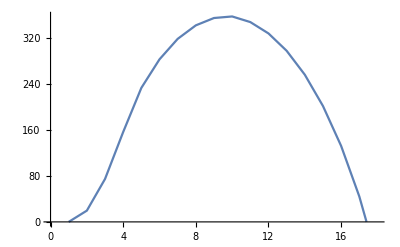

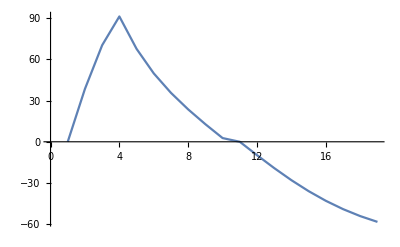

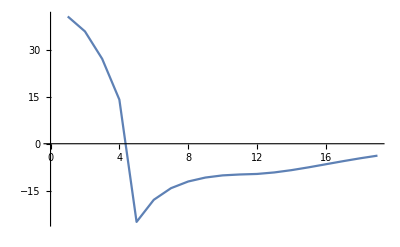

```mathematica
(*this is to create final graph and table*) 
Xpart1=Table[xs[t],{t,0,ttThrust}];
Xpart2=listOfXNT;
Xpart3= listOfX;
PosGraph=Join[Xpart1,Xpart2,Xpart3];

Vpart1=Table[vs[t],{t,0,ttThrust}];
Vpart2=listOfVNT;
Vpart3=Table[VFINALFUNC[t],{t,0,ttFINAL}];
VelGraph=Join[Vpart1,Vpart2,Vpart3];

Apart1=Table[a[t],{t,0,ttThrust}];
Apart2=listOfANT;
Apart3=Table[VFINALFUNC'[t],{t,0,ttFINAL}];
AccGraph=Join[Apart1,Apart2,Apart3];

ListLinePlot[PosGraph,PlotRange->{0,All}]
ListLinePlot[VelGraph]
ListLinePlot[AccGraph]
```